# Clearing variables

This section is used to clear all the variables previously stored in Mathematica

```mathematica
Quiet@Remove["Global`*"]
```

# Auxiliary Functions

This section defines some auxiliary functions used to read LATEX input into Mathematica

```mathematica
FirstEval[term_,innersolnum_,outersolnum_,critchangetemp_]:=Block[{},
auxterm=term/.ToExpression[ToString[par1NF]<>"NF0"]->par1val/.ToExpression[ToString[par1NF]<>"NF2"]->Subscript[par[[1]], 2]/.ToExpression[ToString[par1NF]<>"NF4"]->Subscript[par[[1]], 4]/.ToExpression[ToString[par2NF]<>"NF0"]->par2val/.ToExpression[ToString[par2NF]<>"NF2"]->Subscript[par[[2]], 2]/.ToExpression[ToString[par2NF]<>"NF4"]->Subscript[par[[2]], 4]/.fixedpar/.par1NF->aux1/.par2NF->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par1NF/.aux2->par2NF;
Return[auxterm]
]
FirstOrderEval[term_,phiforC5_,psiforC5_]:=Block[{},
auxterm=term/.Table[ToExpression[ToString[phiNF] <> ToString[coordnum-1]]->phiforC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[psiNF] <> ToString[coordnum-1]]->psiforC5[[coordnum]],{coordnum,nvar}];
Return[auxterm]
]
SecondOrderEval[term_,W02forC5_,W22forC5_]:=Block[{},
auxterm=term/.Table[ToExpression[ToString[W02NF] <> ToString[coordnum-1]]->W02forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W22NF] <> ToString[coordnum-1]]->W22forC5[[coordnum]],{coordnum,nvar}];
Return[auxterm]
]
ThirdOrderEval[term_,W13forC5_,W123forC5_,W133forC5_,W33forC5_]:=Block[{},
auxterm=auxterm/.Table[ToExpression[ToString[W13NF] <> ToString[coordnum-1]]->W13forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W123NF] <> ToString[coordnum-1]]->W123forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W133NF] <> ToString[coordnum-1]]->W133forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W33NF] <> ToString[coordnum-1]]->W33forC5[[coordnum]],{coordnum,nvar}];
Return[auxterm]
]
FourthOrderEval[term_,W04forC5_,W024forC5_,W034forC5_,W24forC5_,W224forC5_,W234forC5_]:=Block[{},
auxterm=term/.Table[ToExpression[ToString[W04NF] <> ToString[coordnum-1]]->W04forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W024NF] <> ToString[coordnum-1]]->W024forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W034NF] <> ToString[coordnum-1]]->W034forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W24NF] <> ToString[coordnum-1]]->W24forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W224NF] <> ToString[coordnum-1]]->W224forC5[[coordnum]],{coordnum,nvar}];
auxterm=auxterm/.Table[ToExpression[ToString[W234NF] <> ToString[coordnum-1]]->W234forC5[[coordnum]],{coordnum,nvar}];
Return[auxterm]
]
Evaluation[term_,order_]:=Block[{},
auxterm=FirstEval[term,innersolnum,outersolnum,critchangetemp];
auxterm=FirstOrderEval[auxterm,phiforC5,psiforC5];
If[order>=2,
auxterm=SecondOrderEval[auxterm,W02forC5,W22forC5];
];
If[order>=3,
auxterm=ThirdOrderEval[auxterm,W13forC5,W123forC5,W133forC5,W33forC5];
];
Return[auxterm]
]
αeval[term_,innersolnum_,outersolnum_,critchangetemp_]:=Block[{},
auxterm=FirstEval[term,innersolnum,outersolnum,critchangetemp];
auxterm=FirstOrderEval[auxterm,phiforC5,psiforC5];
auxterm=SecondOrderEval[auxterm,W02forC5,W22forC5];
auxterm=ThirdOrderEval[auxterm,W13forC5,W123forC5,W133forC5,W33forC5];
auxterm=FourthOrderEval[auxterm,W04forC5,W024forC5,W034forC5,W24forC5,W224forC5,W234forC5];
Return[auxterm/If[Chop[Dot[phiforC5,psiforC5]]!=0,Dot[phiforC5,psiforC5],1]]
]
```

# Vector field

This section loads the List of Kinetics and variables and finds the equilibria of the system if eqbool=1. Otherwise, it only loads Kinetics. This cell requires some input only if Mathematica finds more than one homogeneous steady-state

```mathematica
SetDirectory[NotebookDirectory[]];
eqbool=1;
If[FileExistsQ["Expansion parameters.txt"],
exppar=ToExpression[StringSplit[ReadLine["Expansion parameters.txt"],","]];
par1NF=exppar[[1]];
par2NF=exppar[[2]];
]
Close["Expansion parameters.txt"];
If[FileExistsQ["Kinetics.txt"],
nvar=Length@ReadList["Kinetics.txt",null@String,NullRecords->True];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Kinetics.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
kinetics=Range[nvar];
var=Range[nvar];
For[varnum=1,varnum<=nvar,varnum++,
kinetics[[varnum]]=ToExpression[ReadLine["Kinetics.txt"]];
If[FileExistsQ["List of variables.txt"],
var[[varnum]]=ToExpression[ReadLine["List of variables.txt"]];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'List of variables.txt' was not be found. Run the Python script first."}],"Output"]];
Quit[]
];
]
Close["Kinetics.txt"];
Close["List of variables.txt"];
kinetics=kinetics/.ToExpression[ToString[par1NF] <> "NF0"]->0/.ToExpression[ToString[par2NF] <> "NF0"]->0;
If[eqbool==1,
eqs=Solve[kinetics==0,var];
If[Length[eqs]>1,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Your system has " <> ToString[Length[eqs]] <> " equilibria"}],"Output"]];
For[eqnum=1,eqnum<=Length[eqs],eqnum++,
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Equilibrium number " <> ToString[eqnum] <> " is equal to ",ToString[eqs[[eqnum]],FormatType->StandardForm]}],"Output"]];];
eqnumber=Input["Enter the number of the equilibrium point you would like to consider. Enter 0 if the software did not find your desired homogeneous steady-state or you want to consider them all"];
NotebookClose[aux];
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;]
,
Print["Mathematica found only one homogeneous steady-state in your system. It will proceed with that one."];
eq=eqs[[1]]//Simplify;
]
,
eq={0};
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

# Turing bifurcation variables and Fixed parameters

This section loads the functions required to find and continue Turing bifurcations, and evaluates the parameters that remain fixed throughout the computation

```mathematica
If[FileExistsQ["Third-order coefficient.txt"],
phiNFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
psiNFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W02NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W22NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W13NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W123NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W133NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W33NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W04NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W024NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W034NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W24NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W224NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
W234NFeval=ToExpression[StringSplit[ReadLine["Vectors.txt"],","]];
Close["Vectors.txt"];
C3=ToExpression[Import["Third-order coefficient.txt"]]/.eq;
C3=C3/.Table[ToExpression[ToString[W02NF] <> ToString[coordnum-1]]->W02NFeval[[coordnum]],{coordnum,nvar}];
C3=C3/.Table[ToExpression[ToString[W22NF] <> ToString[coordnum-1]]->W22NFeval[[coordnum]],{coordnum,nvar}];
C3=C3/.Table[ToExpression[ToString[phiNF] <> ToString[coordnum-1]]->phiNFeval[[coordnum]],{coordnum,nvar}];
C3=C3/.Table[ToExpression[ToString[psiNF] <> ToString[coordnum-1]]->psiNFeval[[coordnum]],{coordnum,nvar}];
C3=C3/.ToExpression[ToString[par1NF] <> "NF0"]->par1NF/.ToExpression[ToString[par2NF] <> "NF0"]->par2NF;
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Third-order coefficient.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
If[FileExistsQ["Determinant of the Jacobian matrix.txt"],
zerodet=ToExpression[Import["Determinant of the Jacobian matrix.txt"]]/.eq;
zerodet=zerodet/.ToExpression[ToString[par1NF] <> "NF0"]->par1NF/.ToExpression[ToString[par2NF] <> "NF0"]->par2NF;
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Determinant of the Jacobian matrix.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
If[FileExistsQ["Derivative of the Determinant.txt"],
zeroder=ToExpression[Import["Derivative of the Determinant.txt"]]/.eq;
zeroder=zeroder/.ToExpression[ToString[par1NF] <> "NF0"]->par1NF/.ToExpression[ToString[par2NF] <> "NF0"]->par2NF;
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Derivative of the Determinant.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
If[FileExistsQ["Non-zero variable.txt"],
nonzero=ToExpression[Import["Non-zero variable.txt"]]/.eq;
nonzero=nonzero/.ToExpression[ToString[par1NF] <> "NF0"]->par1NF/.ToExpression[ToString[par2NF] <> "NF0"]->par2NF;
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Non-zero variable.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
If[FileExistsQ["Fixed parameter values.txt"],
Nparametereval=Length@ReadList["Fixed parameter values.txt",null@String,NullRecords->True];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Fixed parameter values.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
fixedpar={};
If[Nparametereval>0,
For[parnum=1,parnum<=Nparametereval,parnum++,
aux=StringSplit[ReadLine["Fixed parameter values.txt"],","];
parname=ToExpression[aux[[1]]];
parval=ToExpression[aux[[2]]];
AppendTo[fixedpar,parname->parval];
];
Close["Fixed parameter values.txt"];
]
```

# Parameters on the axes of the bifurcation diagram

In this section, Mathematica loads the file with the parameters on the axes of the bifurcation diagram and the intervals over which they change

```mathematica
npar=2;
par=Range[npar];
partoformat=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
If[FileExistsQ["Parameters on axes.txt"],
aux=StringSplit[ReadLine["Parameters on axes.txt"],","];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Parameters on axes.txt' was not found. Run the Python script first."}],"Output"]];
Quit[]
];
par[[parnum]]=ToExpression[aux[[1]]];
lowerbound[[parnum]]=ToExpression[aux[[2]]];
upperbound[[parnum]]=ToExpression[aux[[3]]];
]
Close["Parameters on axes.txt"];
If[FileExistsQ["Actual names of parameters.txt"],
aux=StringSplit[ReadLine["Actual names of parameters.txt"],","];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
Close["Actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
];
```

# Bifurcation curves

In this section, this script reads the file “Initial conditions for Turing bifurcation curves” and goes fixing one parameter leaving the other parameter and μ free to solve the two equations that determine a Turing bifurcation curve. Then, the script poses an ordinary differential equation to use the method of pseudo-arclength continuation to continue the bifurcation curves as the parameters change. NOTE: Here, the variable “time” is just an auxiliary variable that can be understood as the arclength of the bifurcation curve but it has nothing to do with the actual time in the reaction-diffusion equation

```mathematica
initialt=-1000;
finalt=1000;
curvespeed=1;
tol=10^-7;
Choptol=10^-7;
smalldifferential=0.001;
zerodetaux=zerodet/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time];
zeroderaux=zeroder/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time];
equations={zerodetaux};
AppendTo[equations,zeroderaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+muNF'[time]^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
equationsGlobalLP={zerodetaux/.muNF[time]->0};
equationsGlobalLP=D[equationsGlobalLP,time];
AppendTo[equationsGlobalLP,(par[[1]]'[time])^2+(par[[2]]'[time])^2-curvespeed^2];
equationsGlobalLP=Table[equationsGlobalLP[[equationnumber]]==0,{equationnumber,Length[equationsGlobalLP]}];
allvar={par[[1]],par[[2]]};
AppendTo[allvar,muNF];
allvartimedependent=Table[allvar[[nvar]][time],{nvar,Length[allvar]}];
allvarGlobalLP=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvarGlobalLP,par[[1]]];
AppendTo[allvarGlobalLP,par[[2]]];
allvarGlobalLPtimedependent=Table[allvarGlobalLP[[nvar]][time],{nvar,Length[allvarGlobalLP]}];
If[FileExistsQ["Initial conditions for Turing bifurcation curves.txt"],
numberofbifurcationcurves=Length@ReadList["Initial conditions for Turing bifurcation curves.txt",null@String,NullRecords->True];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Initial conditions for Turing bifurcation curves.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
initialvalueTuring={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
aux=StringSplit[ReadLine["Initial conditions for Turing bifurcation curves.txt"],","];
AppendTo[initialvalueTuring,{ToExpression[aux[[1]]],ToExpression[aux[[2]]]}];
]
Close["Initial conditions for Turing bifurcation curves.txt"];
solutioncurves={};
solutioncurvesGlobalLP={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueTuring[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
initialvalues=Quiet@NSolve[{zerodet,zeroder}==0/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],{par[[anotherparameter]],muNF}//Evaluate];
initialvaluesGlobalLP=Quiet@NSolve[zerodet==0/.muNF->0/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],par[[anotherparameter]]//Evaluate];
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
initialvalues=DeleteDuplicates[initialvalues];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
If[Activate[Inactivate[Chop[muNF,Choptol]!=0 &&
Max[Abs[{zerodet,zeroder}/.fixedpar]]<tol && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]] && Chop[nonzero/.fixedpar,Choptol]!=0/.initialvalues[[initialsolnum]]],
dereval=Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]->initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]==initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=Quiet@NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[sol]>0 && sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves,sol]
]
]
]
];
initialvaluesGlobalLP=Table[Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]]->Re[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}],{initialsolnum,Length[initialvaluesGlobalLP]}];
initialvaluesGlobalLP=DeleteDuplicates[initialvaluesGlobalLP];
For[initialsolnum=1,initialsolnum<=Length[initialvaluesGlobalLP],initialsolnum++,
AppendTo[initialvaluesGlobalLP[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
If[Activate[Inactivate[Abs[zerodet/.fixedpar/.muNF->0]<tol && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]]/.initialvaluesGlobalLP[[initialsolnum]]],
dereval=Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]][0]->initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equationsGlobalLP/.time->0/.dereval,D[allvarGlobalLPtimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equationsGlobalLP,Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]][0]==initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=Quiet@NDSolve[equationsaux,allvarGlobalLP,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[sol]>0 && sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurvesGlobalLP,sol]
]
]
]
]
]
If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"This script could not find a Turing bifurcation curve or a BD-line for your desired parameters. Try changing tolerances or lines to search."}],"Output"]]]
```

# GLE at codimension-2 points

In this section, the script finds zeroes of the third-order coefficient along Turing bifurcation curves. To do that, it firsts evaluates the C_3 at different points of the bifurcation curves looking for changes of sign. In particular, if the product of C_3 at two different consecutive points is negative, then one of those points si saved to be used as an initial condition to find the actual root of C_3.

```mathematica
Catch[If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
Throw["This script could not find a bifurcation curve for this system"];
,
timedifference=0.01;
disttol=10^-6;
tol=10^-6;
αvals={};
α1NF=ToExpression[Import["alphas/alpha1.txt"]];
α2NF=ToExpression[Import["alphas/alpha2.txt"]];
α3NF=ToExpression[Import["alphas/alpha3.txt"]];
α4NF=ToExpression[Import["alphas/alpha4.txt"]];
α5NF=ToExpression[Import["alphas/alpha5.txt"]];
α6NF=ToExpression[Import["alphas/alpha6.txt"]];
α7NF=ToExpression[Import["alphas/alpha7.txt"]];
υ1NF=ToExpression[Import["alphas/upsilon1.txt"]];
υ2NF=ToExpression[Import["alphas/upsilon2.txt"]];
codimensiontwopoints={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C3/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]);
allvals=Table[{time,auxC3[time]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],timedifference}];
vals={};
For[valnum=1,valnum<=Length[allvals]-1,valnum++,
If[allvals[[valnum]][[2]]*allvals[[valnum+1]][[2]]<0 && allvals[[valnum]][[1]]>solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]] && Chop[muNF[allvals[[valnum]][[1]]]/.solutioncurves[[outersolnum]][[innersolnum]],Choptol]!=0,
AppendTo[vals,allvals[[valnum]][[1]]]
]
];
For[tnum=1,tnum<=Length[vals],tnum++,
initialvalueoft=vals[[tnum]];
critchangetemp=time/.Quiet@FindRoot[auxC3[time],{time,initialvalueoft}];
If[solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=critchangetemp<=solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]] && Abs[auxC3[time]/.time->critchangetemp]<tol && Chop[muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,Choptol]>0,
auxiliaryarray=Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),muNF->(muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp;
AppendTo[codimensiontwopoints,auxiliaryarray];

par1val=par[[1]][critchangetemp]/.solutioncurves[[outersolnum]][[innersolnum]];
par2val=par[[2]][critchangetemp]/.solutioncurves[[outersolnum]][[innersolnum]];

phiforC5=FirstEval[phiNFeval,innersolnum,outersolnum,critchangetemp];
psiforC5=FirstEval[psiNFeval,innersolnum,outersolnum,critchangetemp];

denom=If[Chop[Dot[phiforC5,psiforC5]]!=0,Dot[phiNFeval,psiNFeval]/.ToExpression[ToString[par1NF]<>"NF0"]->par[[1]]/.ToExpression[ToString[par2NF]<>"NF0"]->par[[2]],1];

auxquant=C3/denom/.fixedpar/.par[[1]]->temp/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.temp->par[[1]];
sign=D[auxquant,par[[1]]]/.par[[1]]->par[[1]][time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp;

potentialpars={If[sign>0,Subscript[par[[1]], 2]->1,Subscript[par[[1]], 2]->-1],Subscript[par[[1]], 4]->0};
(*potentialpars={If[sign>0,Subscript[par[[1]], 4]->1,Subscript[par[[1]], 4]->-1],Subscript[par[[1]], 2]->0};*)

W02forC5=Evaluation[W02NFeval,1];
W22forC5=Evaluation[W22NFeval,1];

solvcondeval=Evaluation[υ1NF,2];
solvcondeval=solvcondeval/.ToExpression[ToString[par1NF] <> "NF0"]->par1val/.ToExpression[ToString[par2NF] <> "NF0"]->par2val/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];

If[Variables[solvcondeval/.potentialpars]!={},
soleq=Quiet@Solve[solvcondeval==0/.potentialpars,Variables[solvcondeval/.potentialpars]];
If[Length[soleq]==1,
potentialpars=Join[potentialpars,soleq[[1]]];
]
];

For[counter=1,counter<=Length[potentialpars],counter++,
potentialpars[[counter]][[2]]=(potentialpars[[counter]][[2]]/.potentialpars);
];

W13forC5=Evaluation[W13NFeval,2];
W123forC5=Evaluation[W123NFeval,2];
W133forC5=Evaluation[W133NFeval,2];
W33forC5=Evaluation[W33NFeval,2];

W04forC5=Evaluation[W04NFeval,3];
W024forC5=Evaluation[W024NFeval,3];
W034forC5=Evaluation[W034NFeval,3];
W24forC5=Evaluation[W24NFeval,3];
W224forC5=Evaluation[W224NFeval,3];
W234forC5=Evaluation[W234NFeval,3];

α1eval=αeval[α1NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];
α2eval=αeval[α2NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];
α3eval=αeval[α3NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];
α4eval=αeval[α4NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];
α5eval=αeval[α5NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];
α6eval=αeval[α6NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];
α7eval=αeval[α7NF,innersolnum,outersolnum,critchangetemp]/.potentialpars/.par[[1]]->aux1/.par[[2]]->aux2/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp/.aux1->par[[1]]/.aux2->par[[2]];

β1eval=-(α2eval^2+4 α1eval α5eval)/(4 α1eval^2);
β3eval=-(α2eval (α3eval-α4eval)+2 α1eval α6eval)/(4 α1eval^2);
β5eval=-((α3eval+α4eval) (3 α3eval-5 α4eval)+16 α1eval α7eval)/(48 α1eval^2);

Maxwell=β3eval^2-4 β1eval β5eval/.potentialpars;

If[Variables[Maxwell]!={},
solMaxwell=Quiet@Solve[Maxwell==0,Variables[Maxwell]];
If[Length[solMaxwell]==1,
potentialpars=Join[potentialpars,solMaxwell[[1]]];
]
];

AppendTo[αvals,{{par[[1]][time],par[[2]][time]}/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,{α1eval,α2eval,α3eval,α4eval,α5eval,α6eval,α7eval}//Expand}];
Break[]
]
]
]
];
If[Length[codimensiontwopoints]>0,
codimensiontwopoints=Join[{par[[1]],par[[2]],muNF},var]/.codimensiontwopoints;
codimensiontwopoints=DeleteDuplicates[codimensiontwopoints,EuclideanDistance[##]<disttol&];
critchange=Table[{par[[1]]->codimensiontwopoints[[critnum]][[1]],par[[2]]->codimensiontwopoints[[critnum]][[2]]},{critnum,Length[codimensiontwopoints]}];
codimensiontwopoints=Table[Join[{par[[1]]->codimensiontwopoints[[critnum]][[1]],par[[2]]->codimensiontwopoints[[critnum]][[2]],muNF->codimensiontwopoints[[critnum]][[3]]},Table[var[[varnum]]->codimensiontwopoints[[critnum]][[3+varnum]],{varnum,nvar}]],{critnum,Length[codimensiontwopoints]}];
If[ValueQ[αvals],
auxarr={};
For[critnum=1,critnum<=Length[critchange],critnum++,
getout=0;
For[fifthnum=1,fifthnum<=Length[αvals],fifthnum++,
If[getout==0 && αvals[[fifthnum]][[1]]=={par[[1]],par[[2]]}/.critchange[[critnum]],
AppendTo[auxarr,αvals[[fifthnum]]];
getout=1;
]
]
];
αvals=auxarr;
];
If[ValueQ[αvals] && Length[αvals]>0,Export["αvals at codimension-two bifurcation points.txt",αvals];
,
If[ValueQ[critchange] && Length[critchange]>0,Export["Codimension-two bifurcation points.txt",critchange]];
]
]
]
]
```

# Bifurcation diagram plotting

This section plots each of the parametric bifurcation curves found colored according to the sign of μ and C_3. In particular, if μ>0 and C_3>0 (respectively, C_3<0), then the curve will be coloured Blue (respectively, red). On the othe hand, if μ<0, then the curve will be green dotted. Besides, if μ=0, then the curve will be plotted Gray. Also, if the codimension-two bifurcation points were found in the previous step, they will be plotted in the graph

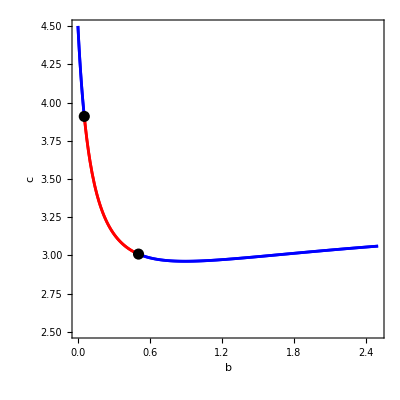

```mathematica
Catch[If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
Throw["This script could not find a bifurcation curve for this system"];
,
If[ValueQ[critchange] && Length[critchange]>=1,
critpoints=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange[[critnum]]]}],{critnum,Length[critchange]}];
];
bifcurveplot={};
GlobalLPplot={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C3/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[{If[Chop[auxnonzero[time],Choptol]!=0 && muNF[time]>0 && auxC3[time]∈Reals && auxC3[time]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && muNF[time]>0 && auxC3[time]∈Reals && auxC3[time]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && muNF[time]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],
If[muNF[time]==0/.solutioncurves[[outersolnum]][[innersolnum]] ,{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Red,Blue,{Green,Dotted},Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[bifcurveplot,tempplot];
]
];
For[outersolnum=1,outersolnum<=Length[solutioncurvesGlobalLP],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurvesGlobalLP[[outersolnum]]],innersolnum++,
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalLP[[outersolnum]][[innersolnum]],{time,solutioncurvesGlobalLP[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurvesGlobalLP[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[GlobalLPplot,tempplot];
]
];
bifcurveplot=Join[bifcurveplot,GlobalLPplot];
CreateDocument[Dynamic[plot2],WindowSize->{500,500}];
If[ValueQ[critpoints],
plot2=Show[bifcurveplot,critpoints,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1] 
,
plot2=Show[bifcurveplot,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
]
]
]
```

```mathematica
taux=NSolve[par[[2]][time]==4.4/.solutioncurves[[1]][[1]],time][[1]];
par[[1]][time]/.solutioncurves[[1]][[1]]/.taux
π/(√muNF[time])/.solutioncurves[[1]][[1]]/.taux
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.0061166

4.97482

```mathematica
4.9748202217244355
```

4.97482

```mathematica
taux=NSolve[par[[1]][time]==2.4/.solutioncurves[[1]][[1]],time][[1]];
par[[2]][time]/.solutioncurves[[1]][[1]]/.taux
π/(√muNF[time])/.solutioncurves[[1]][[1]]/.taux
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

3.05488

5.04724

```mathematica
5.047237434917883
```

5.04724